# Polynomial Interpolation

## Static

-10.2894

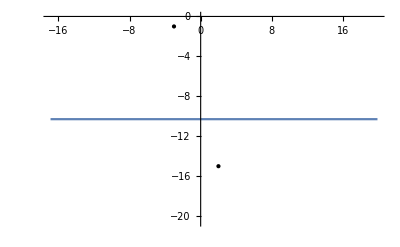

```mathematica
data={{2,-15},{-3,-1},{15,2},{-12,8}};
deg= Length[data]; minx=Min[data⟦All,1⟧];maxx=Max[data⟦All,1⟧];
xr = Sqrt[Total[data⟦All,1⟧^2]]/deg;Table[data⟦j,1⟧^(i-1),{j,deg},{i,deg,1,-1}];
Transpose@Append[Transpose@%,data⟦All,2⟧];
RowReduce[%];
Table[%⟦i,deg+1⟧x^(deg-i),{i,deg}];
Plus@@%
Plot[%,{x,minx-xr,maxx+xr},Epilog->Style[Point[data],Red,PointSize[0.02]]]
```

## Dynamic

```mathematica
Panel[DynamicModule[{data={{1,1},{-1,-1}},c=2,eqn={x}},
Column[{Framed@Style[Dynamic[eqn=
Plus@@(Table[(RowReduce[Transpose[Append[Transpose[Table[Indexed[data,{j,1}]^(i-1),{j,Length[data]},{i,Length[data],1,-1}]],
data⟦All,2⟧]]])⟦k,Length[data]+1⟧x^(Length[data]-k),
{k,Length[data]}])],20,White],
ClickPane[Framed@Dynamic[
Plot[eqn,{x,-10,10},Epilog->Style[Point[data],Red,PointSize[0.02]],ImageSize->{500,500},PlotRange->{-10,10},AspectRatio->1]],(If[Length[data]<c,AppendTo[data,#],data={#}])&],

Framed[Row[{
Style[Dynamic[c],15,White],,
Button[Style["-",LightBlue,15],c--,Enabled->Dynamic[c>2],Background->GrayLevel[0.15],ImageSize->{20,20}],
Button[Style["+",LightRed,15],c++,Enabled->Dynamic[c<8],Background->GrayLevel[0.15],ImageSize->{20,20}]}],
Background->GrayLevel[0.15]]},Center]],Background->GrayLevel[0.15]]
```